# Visualizing Detection Efficiency in Optomechanical Scattering

## Authors: Youssef Tawfik, Thomas Purdy

This file is used to create the theory and main data figures for the paper “Visualizing Detection Efficiency in Optomechanical Scattering”.

## Global Settings/Parameters

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
assumptions={k>0,z>0,A>0,kmx>0, kmy>0,xg>0,x∈Reals,y∈Reals,w0∈PositiveReals};
```

```mathematica
ηQ = 0.875; (*Quantum Efficiency*)
```

## Theory

## Membrane

Mechanical mode function and  u_0(x,y,z=0) which is the scattered field for  A=0, and the scattered mode u_s(x,y,z=0) which is linear in A.

```mathematica
Ψ[x_,y_]=Sin[kmx x] Cos[kmy y] ;
u0[x_,y_]=√(1/(π w0 w0))Exp[-(x)^2/(2 w0^2)]Exp[-(y)^2/(2 w0^2)] ;
us[x_,y_]=2ⅈ Ψ[x,y] u0[x,y];
```

These field are propagated to the far field (z=d>>z_R) into (u^out)_0(x,y) and (u^out)_s(x,y) using the Fraunhofer Approximation.

```mathematica
uout0[x_,y_]=k/(2π ⅈ  z)Integrate[u0[xx,yy] Exp[-I k/z(x xx+y yy)],{xx,-∞,∞},{yy,-∞,∞},Assumptions->assumptions] ;
uouts[x_,y_]=k/(2π ⅈ z) Integrate[us[xx,yy] Exp[-I k/z(x xx+y yy)],{xx,-∞,∞},{yy,-∞,∞},Assumptions->assumptions];
```

The generated far fields are then used to generate the signal and noise integrals 𝒮 and 𝒩 where the detector is defined using a weight function f_w(x,y).

```mathematica
fw[x_,y_]:=(*1-2*UnitStep[x];*)Piecewise[{{1,x<-xg},{-1,x>xg}},0];

𝒩=α^2 Integrate[Abs[uout0[x,y]]^2 fw[x,y]^2,{x,-∞,∞},{y,-∞,∞},Assumptions->assumptions];
𝒮= α^2 k Integrate[(uout0[x,y] Conjugate[uouts[x,y]]+Conjugate[uout0[x,y]] uouts[x,y])fw[x,y],{x,-∞,∞},{y,-∞,∞},Assumptions->assumptions];
```

The ideal and non-ideal measurement imprecision S_A^imp

```mathematica
SAideal=1/(4 α^2 k^2 Integrate[Abs[uouts[x,y]]^2 ,{x,-∞,∞},{y,-∞,∞},Assumptions->assumptions]);
SA=𝒩/𝒮^2;
η=SAideal/SA;
```

Differential detection efficiency dη of a strip of dimensions x : (x->x+dx) and y: (-∞->∞) (Integrate over y)

```mathematica
dηdx[x_]=Integrate[
Refine[α^2 SAideal(2k (𝒮/𝒩)(uout0[x,y] Conjugate[uouts[x,y]]+Conjugate[uout0[x,y]] uouts[x,y])fw[x,y]-(𝒮/𝒩)^2 Abs[uout0[x,y]]^2 fw[x,y]^2)]
,{y,-∞,∞},Assumptions->assumptions];
```

The Ideal differential detection efficiency is

```mathematica
dηdxIdeal[x_]=Integrate[
Refine[4 α^2 k^2 SAideal Abs[uouts[x,y]]^2 ]
,{y,-∞,∞},Assumptions->assumptions];
```

To generate theory plots use the membrane dimensions to generate k_mx,k_my for a given mode (m,n) with a 1064 nm laser.

```mathematica
{kmx1,kmy1}={kmx w0,kmy w0}/.{kmx->1*(2π)/(1500. 10^-6),kmy-> (2π)/(3500. 10^-6),w0->140./(√2)10^-6};

dηdxU[x_]=dηdx[x]//.{z->k w0 wd,kmx->(n/2) kmx1, kmy-> kmy1, w0->1,wd->1};
dηdxIdealU[x_]=dηdxIdeal[x]//.{z->k w0 wd,kmx->(n/2) kmx1, kmy-> kmy1, w0->1,wd->1};
ηU=η//.{z->k w0 wd, kmy->(1/2) kmy1, w0->1,wd->1};

blockfunction[x_]=UnitBox[x/(xb/wd)]/(xb/wd)/.{xb->180. 10^-6,wd->557. 10^-6}; 
dηdxConv[x_]=Convolve[dηdxU[u],blockfunction[u],u,x];
```

Two figures are generated for dη/dx.

Fig 2b is the comparison of different modes

     Fig 2c is the comparison of mode (6,1) with a QPD and a Partially Blocked QPD

```mathematica
Fig2b={
Cases[Plot[dηdxConv[x]/.{n->2,xg->0},{x,-4,4}],Line[pts_]:>pts,Infinity]//First,
Cases[Plot[dηdxConv[x]/.{n->6,xg->0},{x,-4,4}],Line[pts_]:>pts,Infinity]//First,
Cases[Plot[dηdxConv[x]/.{n->10,xg->0},{x,-4,4}],Line[pts_]:>pts,Infinity]//First
};
Fig2f={
Cases[Plot[dηdxConv[x]/.{n->6,xg->0},{x,-4,4}],Line[pts_]:>pts,Infinity]//First,
Cases[Plot[dηdxConv[x]/.{n->6,xg->0.628},{x,-4,4}],Line[pts_]:>pts,Infinity]//First,
Cases[Plot[dηdxIdealU[x]/.n->6,{x,-4,4}],Line[pts_]:>pts,Infinity]//First
};
```

Figure 3 compares the imprecision noise S_A^imp for a QPD and an optimally blocked QPD over a range of mechanical wavenumbers.
 
For each mechanical wavenumber k_m calculate the ideal gap and find the three noise floors S_A imprecision QPD, S_A Optimized QPD both relative to the imprecision of the balanced interferometer measurement.

```mathematica
IdealGap=Interpolation[
Table[{kmx,xg/.FindMaximum[ηU,{xg}][[2]]},{kmx,0.2,5,0.2}]
];
SAInt = 1/(16 α^2 k^2); SFInt=(2ℏ k α)^2;

SAFig3=SA/SAInt//.{z->k w0 wd, kmy->(1/2) kmy1, w0->1,wd->1,xg->0};
SAOptFig3=SA/SAInt//.{z->k w0 wd, kmy->(1/2) kmy1, w0->1,wd->1,xg->IdealGap[kmx]};
SFFig3=(ℏ^2/4)/(SAideal*SFInt)//.{ kmy->(1/2) kmy1, w0->1};
```

```mathematica
Fig3={
Cases[Plot[SAOptFig3,{kmx,0.2,5},PlotRange->All],Line[pts_]:>pts,Infinity]//First,
Cases[Plot[SAFig3,{kmx,0.2,5},PlotRange->All],Line[pts_]:>pts,Infinity]//First,
Cases[Plot[SFFig3,{kmx,0.2,5},PlotRange->All],Line[pts_]:>pts,Infinity]//First
};
```

### Optical Lever Limit

```mathematica
Ψ[x_,y_]=kmx x ;

u0[x_,y_]=√(1/(π w0 w0))Exp[-(x)^2/(2 w0^2)]Exp[-(y)^2/(2 w0^2)] ;
us[x_,y_]=2ⅈ Ψ[x,y] u0[x,y];

uout0[x_,y_]=k/(2π ⅈ  z)Integrate[u0[xx,yy] Exp[-I k/z(x xx+y yy)],{xx,-∞,∞},{yy,-∞,∞},Assumptions->assumptions] ;
uouts[x_,y_]=k/(2π ⅈ z) Integrate[us[xx,yy] Exp[-I k/z(x xx+y yy)],{xx,-∞,∞},{yy,-∞,∞},Assumptions->assumptions];

fw[x_,y_]:=x;

𝒩=α^2 Integrate[Abs[uout0[x,y]]^2 fw[x,y]^2,{x,-∞,∞},{y,-∞,∞},Assumptions->assumptions];
𝒮= α^2 k Integrate[(uout0[x,y] Conjugate[uouts[x,y]]+Conjugate[uout0[x,y]] uouts[x,y])fw[x,y],{x,-∞,∞},{y,-∞,∞},Assumptions->assumptions];
```

```mathematica
SAideal=1/(4 α^2 k^2 Integrate[Abs[uouts[x,y]]^2 ,{x,-∞,∞},{y,-∞,∞},Assumptions->assumptions]);
SA=𝒩/𝒮^2;
η=SAideal/SA;
```

## Dipolar Scatterer

```mathematica
assumptions={δ∈PositiveReals,Θcl∈PositiveReals};
```

Generating the weight function to remove a slit of total arc angle δ out of the far field around the x and y axes.

```mathematica
wx[δ_,θ_,ϕ_]:=Piecewise[
{
{1,Sin[θ]Cos[ϕ]>Sin[δ/2]},
{-1,Sin[θ]Cos[ϕ]<-Sin[δ/2]}
},0]
wy[δ_,θ_,ϕ_]:=Piecewise[
{
{1,Sin[θ]Sin[ϕ]>Sin[δ/2]},
{-1,Sin[θ]Sin[ϕ]<-Sin[δ/2]}
},0]
```

Calculating signal and noise by integrating over different regions in the far field with a weight function

```mathematica
𝒮x[δ_,Θcl_]:=1/π √(3/2) NIntegrate[2wx[δ,θ,ϕ](Sin[ϕ]^2+Cos[ϕ]^2 Cos[θ])Sin[θ]^2 Cos[ϕ] √Cos[θ],{ϕ,-π/2,π/2},{θ,δ/2,Θcl}]
𝒩x[δ_,Θcl_]:=1/π NIntegrate[2 wx[δ,θ,ϕ]^2 Cos[θ]Sin[θ],{ϕ,-π/2,π/2},{θ,δ/2,Θcl}];

𝒮y[δ_,Θcl_]:=1/π √(3/2) NIntegrate[2wy[δ,θ,ϕ](Sin[ϕ]^2+Cos[ϕ]^2 Cos[θ])Sin[θ]^2 Sin[ϕ] √Cos[θ],{ϕ,0,π},{θ,δ/2.,Θcl}]
𝒩y[δ_,Θcl_]:=1/π NIntegrate[2 wy[δ,θ,ϕ]^2 Cos[θ]Sin[θ],{ϕ,0,π},{θ,δ/2,Θcl}]
```

Generating plots for η_y for different NA collection lenses with and without a block in the QPD

Fig 4b: Plotting η_y vs block angle for different NA

```mathematica
NAclList={0.6,0.8,0.9,1.0};
Fig4b=Table[Cases[
Plot[5/8*𝒮y[δ,ArcSin[NAclList[[i]]]]^2/𝒩y[δ,ArcSin[NAclList[[i]]]],{δ,0.,π}]
,Line[pts_]:>pts,Infinity]//First
,{i,Length[NAclList]}];
```

Generating plots for η_y for different NA collection lenses with and without a block in the QPD

Fig 4c: Plotting the η_y for an optimally blocked QPD

```mathematica
ηyListQPD=Cases[
Plot[5/8*𝒮y[0,ArcSin[NAcl]]^2/𝒩y[0,ArcSin[NAcl]],{NAcl,0.,1.}]
,Line[pts_]:>pts,Infinity]//First;
```

```mathematica
ηyListOptQPD=Table[
{NAcl,FindMaximum[5/8*𝒮y[δ,ArcSin[NAcl]]^2/𝒩y[δ,ArcSin[NAcl]],{δ,0.5,0.2,1.1}]//First}
,{NAcl,0.5,1.,0.01}];
```

```mathematica
Fig4c={ηyListQPD,ηyListOptQPD,
Cases[Plot[1/1024(512-570Cos[ArcSin[NAcl]]+55Cos[3ArcSin[NAcl]]+3Cos[5ArcSin[NAcl]]),{NAcl,0,1.},PlotRange->All],Line[pts_]:>pts,Infinity]//First
};
```

Differential detection efficiency plots

```mathematica
dηydΩ[θ_,ϕ_]=15/(16π)(2(𝒮y[0,π/2]/𝒩y[0,π/2])√Cos[θ] Sin[θ]Sin[ϕ](Sin[ϕ]^2+Cos[ϕ]^2 Cos[θ])wy[0,θ,ϕ]-(𝒮y[0,π/2]/𝒩y[0,π/2])^2 Cos[θ] wy[0,θ,ϕ]^2);
```

```mathematica
SphericalPlot3D[dηydΩ[θ,ϕ],{θ,0,π/2},{ϕ,0,2π},ColorFunction->Function[{x,y,z,θ,ϕ,r},Piecewise[{{RGBColor[0.37, 0.439207, 1.],dηxdΩ[θ,ϕ]>0},{RGBColor[0.909804, 0.0666667, 0.176471],dηxdΩ[θ,ϕ]<0}}]]]
```

```mathematica
PolarPlot[Abs[dηydΩ[θ,π/2]],{θ,-π,π},PolarAxes->True,ColorFunction->Function[{θ,ϕ},Piecewise[{{RGBColor[0.37, 0.439207, 1.],dηydΩ[θ,π/2]>0},{RGBColor[0.909804, 0.0666667, 0.176471],dηydΩ[θ,π/2]<0}}]]]
```

```mathematica
Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\paperfigures\\fig5polar.svg",
PolarPlot[dηydΩ[θ,π/2],{θ,-π/2,π/2},PolarAxes->True],"SVG"
]
```

Z:\User\Youssef\measurement_efficiency\Publication_Files\Figures\paperfigures\fig5polar.svg

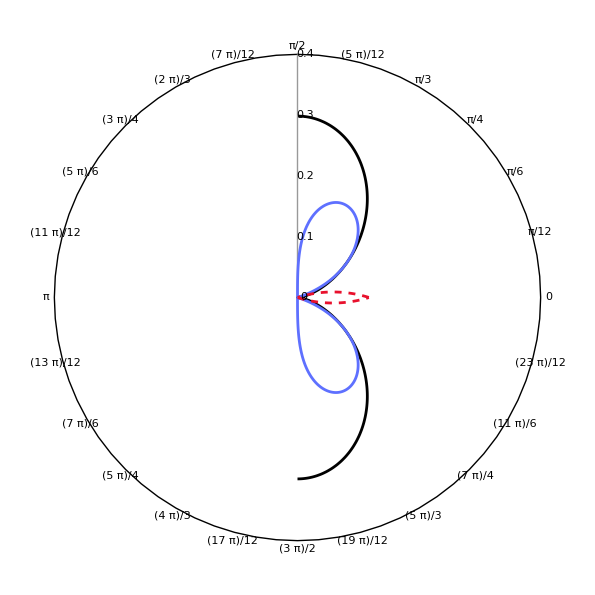

```mathematica
Show[
PolarPlot[
15/(16π)(1-Sin[θ]^2 Cos[π/2]^2)Sin[θ]^2 Sin[π/2]^2
,{θ,-π/2,π/2},PolarAxes->True,PlotStyle->Black],

PolarPlot[
Piecewise[{
{dηydΩ[θ,π/2],dηydΩ[θ,π/2]>0},
{None,dηydΩ[θ,π/2]<=0}
}],{θ,-π/2,π/2},Axes->None,PlotStyle->RGBColor[0.37, 0.439207, 1.]],

PolarPlot[
Piecewise[{
{-dηydΩ[θ,π/2],dηydΩ[θ,π/2]<0},
{None,dηydΩ[θ,π/2]<=0}
}],{θ,-π/2,π/2},Axes->None,PlotStyle->{RGBColor[0.909804, 0.0666667, 0.176471],Dashed}],PlotRange->All
]
```

## Data

### Thermal data

Four thermal spectra are taken with each block size (no block, 0.5 mm block, 0.7 mm block, 1 mm block). 

For each of these thermal spectra the dark noise is subtracted and the five modes are calibrated to units of m^2/Hz and noise floor extracted and placed into the files (sxmatrix0, sxmatrix1, sxmatrix2, sxmatrix3) corresponding to the four block sizes.

The total power reflected from the membrane for each of these runs was (0.711 mW, 1.31 mW, 2.22 mW, 2.27 mW) respectively.

Collected data

```mathematica
SAMatrix = {
 Import["Data\\thermalplots\\block0\\sxmatrix0.csv","SkipLines"->2]//Transpose,
 Import["Data\\thermalplots\\block1\\sxmatrix1.csv","SkipLines"->2]//Transpose,
 Import["Data\\thermalplots\\block2\\sxmatrix2.csv","SkipLines"->2]//Transpose,
 Import["Data\\thermalplots\\block3\\sxmatrix3.csv","SkipLines"->2]//Transpose
};

SAMatrix = Table[Mean[SAMatrix[[i,j,All]]],{i,4},{j,5}]/2;(*Multiplying by two to compare to two sided spectra*)
TotalPower = {0.711,1.31,2.22,2.27}*10^-3(*Watts*);
αList=√(TotalPower/ℏω)/.{ℏω->1.86696 10^-19};
modes={2,4,6,8,10};
```

The numerical values of S_A^ideal are calculated in m^2/Hz to compare to the values of the noise floor obtained from spectra.

```mathematica
SidealExp=SAideal/.{kmx->(n/2)kmx1,kmy->kmy1,k->(2π)/(1064. 10^-9),w0->1};
ηMatrix=Table[(SidealExp/.{n->modes[[j]],α->αList[[i]]})/SAMatrix[[i,j]],{i,Length[SAMatrix]},{j,Length[SAMatrix[[1]]]}];
```

### Fig 2b

Data is taken with a strong drive on the membrane near the relevant modes. The signal to noise is extracted by comparing the value of the spectral peak to the noise floor in IGOR. This data is saved in the files (detadx_mode2  ,detadx_mode2, detadx_mode2).

Extracting this data and converting it to η.

```mathematica
ηNoBlock=ηMatrix[[1,{1,3,5}]];
WireSize=(xb/wd)/.{xb->180. 10^-6,wd->557. 10^-6};

SNRsweeps={
Import["Data\\gapless_sweep\\detadx_mode2.csv","SkipLines"->1],
Import["Data\\gapless_sweep\\detadx_mode6.csv","SkipLines"->1],
Import["Data\\gapless_sweep\\detadx_mode10.csv","SkipLines"->1]
};

xlist=SNRsweeps[[All,All,1]];
snrlist=SNRsweeps[[All,All,2]];
```

The first and last point of the lists correspond to an unblocked QPD, we know what the value of η should be in that case (from our calibrated thermal data). Scaling all points by this value to convert SNR to η and subtracting all points from η_0 to get the change in η upon blocking point x

```mathematica
Do[
snrlist[[i]] =1/ηQ(ηNoBlock[[i]]-snrlist[[i]]*ηNoBlock[[i]]/Mean[snrlist[[i]][[{1,-1}]]])/WireSize;
,{i,Length[snrlist]}]
```

```mathematica
Fig2bData = Table[{xlist[[i,j]],snrlist[[i,j]]},{i,Length[xlist]},{j,Length[xlist[[i]]]}];
```

### Fig 2f

```mathematica
ηNoBlock=ηMatrix[[{1,3},3]] ;
WireSize=(xb/wd)/.{xb->180. 10^-6,wd->557. 10^-6};

SNRsweeps={
Import["Data\\gaped_sweep\\detadx_mode6_nogap.csv","SkipLines"->1],
Import["Data\\gaped_sweep\\detadx_mode6_idealgap.csv","SkipLines"->1]
};

xlist=SNRsweeps[[All,All,1]];
snrlist=SNRsweeps[[All,All,2]];

(*Scale the unblocked point of each sweep to its known value of η*)
Do[
snrlist[[i]] =1/ηQ(ηNoBlock[[i]]-snrlist[[i]]*ηNoBlock[[i]]/Mean[snrlist[[i]][[{1,-1}]]])/WireSize;
,{i,Length[snrlist]}]
```

```mathematica
Fig2fData = Table[{xlist[[i,j]],snrlist[[i,j]]},{i,Length[xlist]},{j,Length[xlist[[i]]]}];
```

### Fig 2d

```mathematica
ηNoBlock=ηMatrix[[1,{1,3,5}]];

snrgaps={
Drop[Import["Data\\eta_block\\snr_gap_2.csv"],1],
Drop[Import["Data\\eta_block\\snr_gap_6.csv"],1],
Drop[Import["Data\\eta_block\\snr_gap_10.csv"],1]
};

Do[
snrgaps[[i,All,2]]*=(ηNoBlock[[i]]/snrgaps[[i,1,2]])
,{i,Length[snrgaps]}]
```

```mathematica
Fig2dData=snrgaps;
```

### Fig 3

For each measured mode k_m find the lowest measured noise floor divide it by the noise floor of an interferometer operating at the same input power.

```mathematica
SAMatrixScaled=Table[SAMatrix[[i,j]]/SAInt/.{k->(2π)/(1064. 10^-9),α->αList[[i]]},{i,4},{j,5}]*ηQ;
IdealBlockIndex=Table[PositionSmallest[SAMatrixScaled[[All,j]]],{j,5}]//Flatten;
SAIdealGap=Table[Min[Transpose[SAMatrixScaled][[mode]]],{mode,Length[modes]}];
SANoGap=SAMatrixScaled[[1]];

Fig3Data={
SANoGapFig3 =  Table[{modes[[i]]/2 kmx1, SANoGap[[i]]},{i,Length[modes]}]/.k->(2π)/(1.064 10^-6),
SAIdealFig3 =  Table[{modes[[i]]/2 kmx1, SAIdealGap[[i]]},{i,Length[modes]}]/.k->(2π)/(1.064 10^-6)
};
```

## Plots

```mathematica
color=ColorData[116,"ColorList"];
```

### Figure 2

#### Fig2b

```mathematica
xticks={{-3,""},{-1,""},{1,""},{3,""}};
yticks={{-0.2,""},{0,""},{0.2,""}};
ticks= {xticks,yticks};
width = 1.65 * 72;height = 0.8*72;
plotmarkers={Graphics[{Disk[]},ImageSize->3],Graphics[Rectangle[],ImageSize->3],Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],ImageSize->3]};


Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\vectorgraphics\\Fig2b.svg",
Show[
ListPlot[Fig2bData,PlotMarkers->plotmarkers],
ListLinePlot[Fig2b,PlotStyle->Thickness[0.005],PlotRange->All],
Frame->True,FrameTicks->ticks,AspectRatio->height/width,ImageSize->{width,height},ImagePadding->None,PlotRange->All
]
]
```

Z:\User\Youssef\measurement_efficiency\Publication_Files\Figures\vectorgraphics\Fig2b.svg

#### Fig2f

```mathematica
xticks={{-3,""},{-1,""},{1,""},{3,""}};
yticks={{-0.2,""},{0,""},{0.2,""}};
ticks= {xticks,yticks};
width = 1.65 * 72;height = 0.8*72;
plotmarkers={Graphics[Polygon[{{1/√2,0},{0,1/√2},{-1/√2,0},{0,-1/√2}}],ImageSize->4],Graphics[{Rectangle[]},ImageSize->3]};

Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\vectorgraphics\\Fig2f.svg",
Show[
ListLinePlot[Fig2f,PlotStyle->Thickness[0.005],PlotRange->All],
ListPlot[Fig2fData,PlotRange->All,PlotMarkers->plotmarkers],
Frame->True,FrameTicks->ticks,AspectRatio->height/width,ImageSize->{width,height},ImagePadding->None,PlotRange->All
]
]
```

Z:\User\Youssef\measurement_efficiency\Publication_Files\Figures\vectorgraphics\Fig2f.svg

```mathematica
Graphics[Polygon[{{1/√2,0},{0,1/√2},{-1/√2,0},{0,1/√2}}]]
```

-Graphics-

#### Fig2d

```mathematica
xticks={{0,""},{1,""},{2,""},{3,""},{4,""}};
yticks={{0,""},{0.1,""},{0.2,""},{0.3,""},{0.4,""},{0.5,""},{0.6,""}};
ticks= {xticks,yticks};
width = 1.65 * 72;height = 0.8*72;

Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\vectorgraphics\\Fig2d.svg",
ListPlot[Fig2dData,
Frame->True,FrameTicks->ticks,AspectRatio->height/width,ImageSize->{width,height},ImagePadding->None,PlotRange->All,PlotMarkers->plotmarkers]
]
```

Z:\User\Youssef\measurement_efficiency\Publication_Files\Figures\vectorgraphics\Fig2d.svg

### Figure 3

```mathematica
xticks={{0.2,""},{0.5,""},{1,""},{2,""},{5,""}};
yticks={{0.1,""},{1,""},{10,""},{100,""}};
ticks= {Log[xticks],Log[yticks]};
width = 2.14* 72;height =1.6*72;
plotmarkers={Graphics[{Disk[]},ImageSize->6],Graphics[Rectangle[],ImageSize->6],Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],ImageSize->6]};

Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\vectorgraphics\\Fig3.svg",
Show[
ListLogLogPlot[Fig3Data,PlotStyle->{{color[[2]]},{color[[1]]}},PlotMarkers->plotmarkers],
ListLogLogPlot[Fig3,Joined->True,PlotRange->{0.01,200}],
Frame->True,FrameTicks->ticks,AspectRatio->height/width,ImageSize->{width,height},ImagePadding->None,PlotRange->Log[{0.01,140}],Axes->False
]
]
```

Z:\User\Youssef\measurement_efficiency\Publication_Files\Figures\vectorgraphics\Fig3.svg

### Figure 4

```mathematica
xticks=Table[{n,""},{n,0,3,0.5}];
yticks=Table[{n,""},{n,0,0.35,0.05}];
ticks = {xticks,yticks};
width =2* 72;height =1.25*72;

Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\vectorgraphics\\Fig4b.svg",
ListLinePlot[Fig4b,
PlotStyle->Black,Frame->True,FrameTicks->ticks,AspectRatio->height/width,ImageSize->{width,height},ImagePadding->None,Axes->False]
]
xticks=Table[{n,""},{n,0,1,0.2}];
yticks=Table[{n,""},{n,0,0.5,0.1}];
ticks = {xticks,yticks};

Export["Z:\\User\\Youssef\\measurement_efficiency\\Publication_Files\\Figures\\vectorgraphics\\Fig4c.svg",
ListLinePlot[Fig4c,
PlotStyle->{color[[3]],{color[[3]],Dashed},Black},Frame->True,FrameTicks->ticks,AspectRatio->height/width,ImageSize->{width,height},ImagePadding->None,Axes->False,PlotRange->All]
];
```

Z:\User\Youssef\measurement_efficiency\Publication_Files\Figures\vectorgraphics\Fig4b.svg